```mathematica
edges= {{13,27},{13,28},{13,18},{27,1},{27,9},{25,32},{25,34},{25,4},{32,24},{32,30},{26,33},{26,31},{26,37},{33,6},{33,19},{15,36},{15,20},{15,16},{36,10},{36,21},{6,5},{6,2},{23,31},{23,12},{23,29},{31,8},{20,38},{20,17},{38,9},{38,37},{22,29},{22,34},{22,30},{29,3},{3,37},{3,8},{2,11},{2,14},{11,18},{11,21},{14,4},{14,12},{19,9},{19,1},{0,35},{0,28},{0,12},{35,17},{35,30},{17,39},{39,10},{39,34},{10,28},{7,16},{7,21},{7,24},{16,18},{1,8},{24,5},{4,5}};
```

```mathematica
g =Graph[Table[UndirectedEdge[edges[[i,1]],edges[[i,2]]],{i,1,Dimensions[edges][[1]]}]];
```

```mathematica
FindMinimumCut[g]
```

{3,{{7},{13,27,28,18,1,9,25,32,34,4,24,30,26,33,31,37,6,19,15,36,20,16,10,21,5,2,23,12,29,8,38,17,22,3,11,14,0,35,39}}}

```mathematica
FindGraphPartition[g]
```

{{13,28,18,25,32,34,24,30,15,36,20,16,10,21,17,22,11,35,39,7},{27,1,9,4,26,33,31,37,6,19,5,2,23,12,29,8,38,3,14,0}}

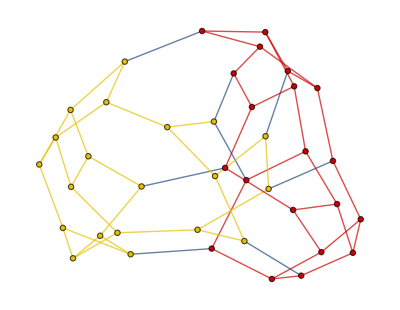

```mathematica
HighlightGraph[g,Map[Subgraph[g,#]&,%]]
```

```mathematica
Dimensions[{13,28,18,25,32,34,24,30,15,36,20,16,10,21,17,22,11,35,39,7}]
```

{20}

```mathematica
ed4={{25,32},{25,38},{25,16},{25,30},{32,33},{32,35},{32,23},{7,26},{7,5},{7,2},{7,8},{26,20},{26,35},{26,17},{15,39},{15,36},{15,31},{15,37},{39,30},{39,17},{39,6},{20,38},{20,24},{20,17},{38,21},{38,14},{5,19},{5,9},{5,18},{19,3},{19,16},{19,28},{23,34},{23,0},{23,22},{34,4},{34,30},{34,36},{0,14},{0,29},{0,8},{14,21},{14,18},{2,11},{2,8},{2,28},{11,37},{11,27},{11,10},{30,33},{1,33},{1,17},{1,13},{1,27},{33,31},{12,36},{12,9},{12,35},{12,10},{36,16},{13,28},{13,37},{13,27},{28,31},{18,21},{18,3},{21,22},{37,24},{24,10},{24,22},{31,29},{9,16},{9,6},{4,8},{4,35},{4,3},{27,29},{29,6},{3,10},{22,6}};
```

```mathematica
g =Graph[Table[UndirectedEdge[ed4[[i,1]],ed4[[i,2]]],{i,1,Dimensions[ed4][[1]]}]];
```

```mathematica
FindGraphPartition[g]
```

{{30,33,26,2,20,17,15,39,31,37,6,24,28,22,29,11,27,10,1,13},{25,32,38,16,35,23,7,5,8,36,21,14,19,9,18,3,34,0,4,12}}

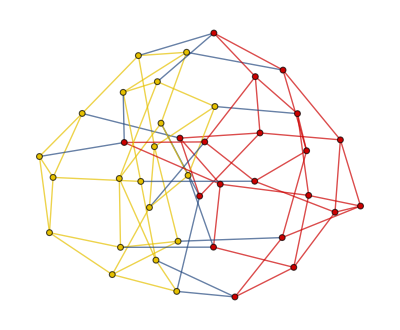

```mathematica
HighlightGraph[g,Map[Subgraph[g,#]&,%]]
```

```mathematica
16
```

16

so exactly good for epsilon =0.1